```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zakk/Desktop/ISTAustria/DynamicsSC/Tenth

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zakk/Desktop/ISTAustria/DynamicsSC/Tenth

```mathematica
MyImport[fname_]:=Cases[Import[fname,"Table"],{_?NumberQ,___}];
```

```mathematica
{mint,maxt}={-40,80};
```

```mathematica
<<RootSearch.m
```

```mathematica
GetEnergy[idata_]:=With[{data=With[{int=Interpolation[{#[[1]],#[[2]]}&/@idata,InterpolationOrder->2]},Quiet@RootSearch[int[x]==0,{x,mint,maxt},InitialSamples->5000]]},data]
```

```mathematica
fname="test_xx_1500/"<>"dsc.norms.dat";
```

```mathematica
fname0="test_xx_1500/"<>"dsc.outg.0.dat";
```

```mathematica
fname2="test_xx_1500/"<>"dsc.outg.2.dat";
```

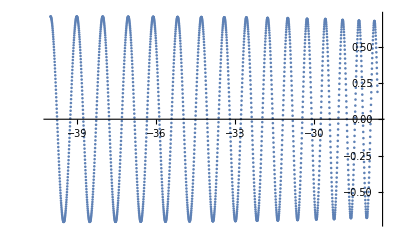

```mathematica
ListPlot[{#[[1]],#[[2]]}&/@MyImport[fname2]]
```

```mathematica
ramp=Drop[With[{data=MyImport[fname]},With[{idx=Length[data[[1]]]},{#[[1]],#[[idx]]}&/@data]],1];
```

```mathematica
EnL0=Join[{{-40,0}},{(#[[1]]+#[[2]])/2,π*(#[[2]]-#[[1]])^-1}&/@Partition[x/.GetEnergy[{#[[1]],#[[2]]}&/@MyImport[fname0]],2]];
```

```mathematica
EnL2={(#[[1]]+#[[2]])/2,π*(#[[2]]-#[[1]])^-1}&/@Partition[x/.GetEnergy[{#[[1]],#[[2]]}&/@MyImport[fname2]],2];
```

InterpolatingFunction::dmval: Input value {-39.9997} lies outside the range of data in the interpolating function. Extrapolation will be used.

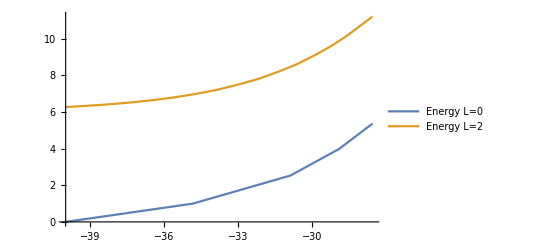

```mathematica
With[{intL0=Interpolation[EnL0,InterpolationOrder->1],intL2=Interpolation[EnL2,InterpolationOrder->1],intramp=Interpolation[ramp]},Plot[{intL0[x],intL2[x]},{x,Min[#[[1]]&/@EnL0],Max[#[[1]]&/@EnL0]},PlotLegends->{"Energy L=0","Energy L=2"}]]
```

InterpolatingFunction::dmval: Input value {-39.9997} lies outside the range of data in the interpolating function. Extrapolation will be used.

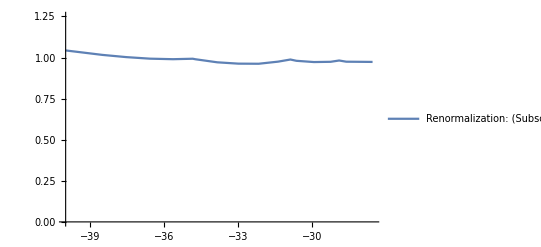

```mathematica
With[{intL0=Interpolation[EnL0,InterpolationOrder->1],intL2=Interpolation[EnL2,InterpolationOrder->1]},Plot[{(intL2[x]-intL0[x])/6},{x,Min[#[[1]]&/@EnL0],Max[#[[1]]&/@EnL0]},PlotLegends->{"Renormalization: (SubscriptBox[E, L = 2] - SubscriptBox[E, L = 0])/6"},PlotRange->{{Min[#[[1]]&/@EnL0],Max[#[[1]]&/@EnL0]},{0,1.25}}]]
```

```mathematica
qpw0={#[[1]],#[[4]]}&/@MyImport[fname0];
```

```mathematica
qpw2={#[[1]],#[[4]]}&/@MyImport[fname2];
```

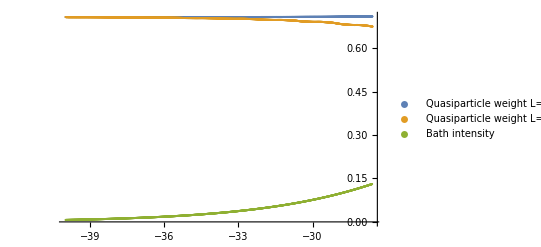

```mathematica
ListPlot[{qpw0,qpw2,ramp},PlotLegends->{"Quasiparticle weight L=0","Quasiparticle weight L=2","Bath intensity"}]
```

This is not 1500, it’s 500!

```mathematica
fname="test_nadab_1500/"<>"dsc.norms.dat";
```

```mathematica
fname0="test_nadab_1500/"<>"dsc.outg.0.dat";
```

```mathematica
fname2="test_nadab_1500/"<>"dsc.outg.2.dat";
```

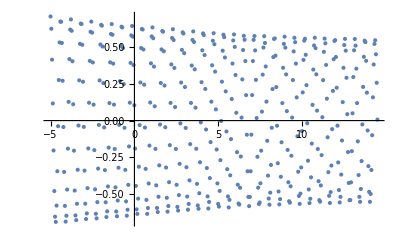

```mathematica
ListPlot[{#[[1]],#[[2]]}&/@MyImport[fname2]]
```

```mathematica
ramp=Drop[With[{data=MyImport[fname]},With[{idx=Length[data[[1]]]},{#[[1]],#[[idx]]}&/@data]],1];
```

```mathematica
EnL0=Join[{(#[[1]]+#[[2]])/2,π*(#[[2]]-#[[1]])^-1}&/@Partition[x/.GetEnergy[{#[[1]],#[[2]]}&/@MyImport[fname0]],2]];
```

```mathematica
EnL2={(#[[1]]+#[[2]])/2,π*(#[[2]]-#[[1]])^-1}&/@Partition[x/.GetEnergy[{#[[1]],#[[2]]}&/@MyImport[fname2]],2];
```

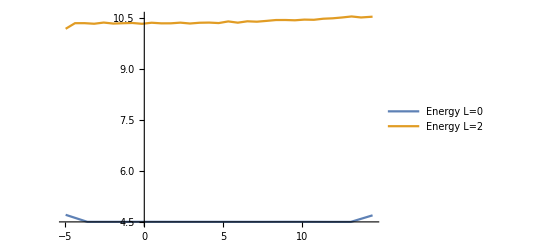

```mathematica
With[{intL0=Interpolation[EnL0,InterpolationOrder->1],intL2=Interpolation[EnL2,InterpolationOrder->1],intramp=Interpolation[ramp]},Plot[{intL0[x],intL2[x]},{x,Min[#[[1]]&/@EnL0],Max[#[[1]]&/@EnL0]},PlotLegends->{"Energy L=0","Energy L=2"}]]
```

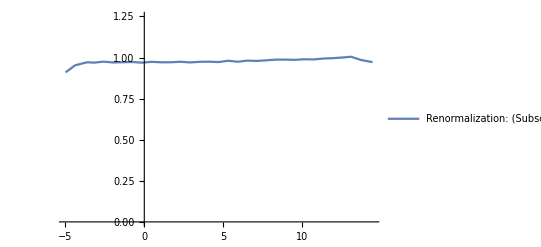

```mathematica
With[{intL0=Interpolation[EnL0,InterpolationOrder->1],intL2=Interpolation[EnL2,InterpolationOrder->1]},Plot[{(intL2[x]-intL0[x])/6},{x,Min[#[[1]]&/@EnL0],Max[#[[1]]&/@EnL0]},PlotLegends->{"Renormalization: (SubscriptBox[E, L = 2] - SubscriptBox[E, L = 0])/6"},PlotRange->{{Min[#[[1]]&/@EnL0],Max[#[[1]]&/@EnL0]},{0,1.25}}]]
```

```mathematica
qpw0={#[[1]],#[[4]]}&/@MyImport[fname0];
```

```mathematica
qpw2={#[[1]],#[[4]]}&/@MyImport[fname2];
```

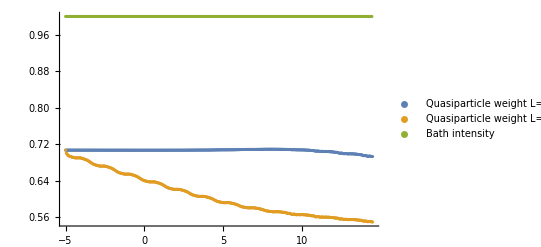

```mathematica
ListPlot[{qpw0,qpw2,ramp},PlotLegends->{"Quasiparticle weight L=0","Quasiparticle weight L=2","Bath intensity"}]
```